```mathematica
path = NotebookDirectory[]<>"/images/";
path2=NotebookDirectory[]<>"VesicleImage";

imageFiles=FileNames["*.png",path2];

bigImage = Import[path<>"EM.jpg"];

bigImages=Import[#]&/@imageFiles;
(*template =Import[path<>"template2.jpg"];*)
bigTemplate =Import[path<>"template.jpg"];

ImageDimensions[template]

TakeChannel[img_]:=ColorSeparate[img][[1]]
MaxIntensity[img_]:=Position[ImageData@ImageReflect@ImageAdjust@img,1.0];
DrawPointAt[x_,y_]:=Graphics[{Red,PointSize[Large],Point[{x,y}]}];

image=TakeChannel[bigImage];
images=TakeChannel[#]&/@bigImages;
template=TakeChannel[bigTemplate];
```

## Determine Propability Distribution of Static Noise

```mathematica
dist=EmpiricalDistribution@ImageLevels@images[[#]]&/@Table[i,{i,1,Length[images],1}];

noiseIm=RandomImage[dist[[#]],{150,150},ColorSpace->"Grayscale"]&/@Table[i,{i,1,Length[images],1}];
(*Round[.5*ImageDimensions@images[[#]]]*)
```

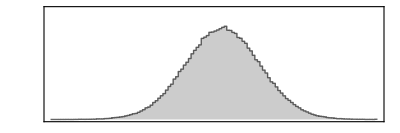

```mathematica
ImageHistogram[images[[1]],PlotRange->{0,8000}]
```

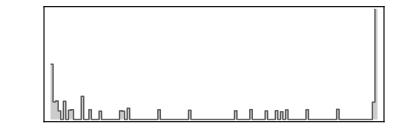

```mathematica
ImageHistogram@noiseIm[[1]]
```

Now we can look at a smattering of the outputs.
They all look basically the same, but it isn’t too expensive, so we may as well compute them individually.
Not sure why the histograms come out so strangely....

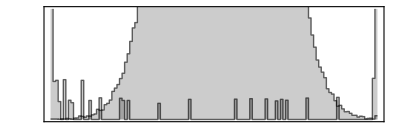
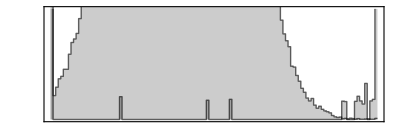
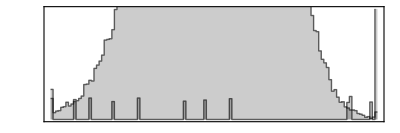
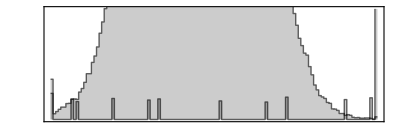
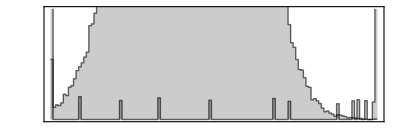
{-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-}

```mathematica
(*Grid[{
{images[[#]]}
,
{ImageHistogram[images[[#]]]}
,
{noiseIm[[#]]}
,
{ImageHistogram[noiseIm[[#]]]}
}]&/@Table[i,{i,1,9,1}]
*)
Grid[{
{images[[#]]}
,
{noiseIm[[#]]}
,
{Show[{
ImageHistogram[noiseIm[[#]],PlotRange->{0,500}],
ImageHistogram[images[[#]]]
}
]}
}]&/@Table[i,{i,1,5,1}]
```

## Template Array

Thickness should be thicker than that actual feature, so as the spread out the convolved peak, making it easier to find.

```mathematica
thickness=0.01;
rMin=45;
rMax=75;
dr=5;
```

```mathematica
templates=Show[
noiseIm[[1]],
Graphics[{GrayLevel[.3],Thickness[thickness],Circle[.5*ImageDimensions[noiseIm[[1]]],#]}]
]&/@Table[j,{j,rMin,rMax,dr}];

(* &[Table[i,{i,1,4,1}] *)
```

```mathematica
Grid[{templates[[1;;4]]}]
Grid[{images[[1;;4]]}]
```

## Perform Convolutions

It appears that the image and template are reversed in the only working orientation. Presumably,

```mathematica
conv=ImageCorrelate[images[[1]],templates[[1]],CorrelationDistance,PerformanceGoal->"Speed",Padding->"Fixed"]&/@Table[i,{i,1,3,1}];
```

```mathematica
ImageDimensions[conv[[1]]]
```

{494,491}

```mathematica
Show[{images[[8]],templates[[6]]}]
```

## No Convolutions Here

This script performs the following algorithm

### FFT, Gaussian removal of HF noise, IFFT

### Radon (~Hough) Transform, filters with Ramp Filter with Constant Slope (#&) ImageDimensions forces the output of InverseRadon to be the same as the original image

### DeleteSmallComponents cleans things up, then a Morphological Binarize pulls out the circle.

### ComponentMeasurements finds the centroid and radius of the circle

```mathematica
dims=ImageDimensions[#]&/@images
```

{{494,491},{495,492},{496,495},{497,496},{496,496},{497,495},{497,494},{507,507},{507,509},{497,496},{496,495},{495,495},{497,495},{497,497},{497,497},{498,494},{509,509},{510,508},{495,494}}

```mathematica
xdims=dims[[#,1]]&/@Table[i,{i,1,Length@images,1}];
ydims=dims[[#,2]]&/@Table[i,{i,1,Length@images,1}];
```

```mathematica
ims=ImageData[#]&/@images;
fft=Fourier[#]&/@ims;
```

```mathematica
(*ListDensityPlot[Abs[#],PlotRange->{0,100}]&/@fft*)
```

Standard deviations of the Gaussians in the x and y directions.

```mathematica
σxs=40.0;σys=35.;
```

```mathematica
mask=Compile[{},Outer[Times,Exp[-(Range[#]-#/2)^2/(2 σys^2)]&/@(ydims),Exp[-(Range[#]-#/2)^2/(2 σxs^2)]&/@(xdims)]];
```

```mathematica
maskr=RotateLeft[#,Floor[#]&/@(dims/2)]&/@mask[]
```

RotateLeft::rspec: Rotation specification {{247, 245}, {247, 246}, {248, 247}, {248, 248}, {248, 248}, {248, 247}, {248, 247}, {253, 253}, {253, 254}, {248, 248}, {248, 247}, {247, 247}, {248, 247}, {248, 248}, {248, 248}, {249, 247}, {254, 254}, {255, 254}, {247, 247}} should be a machine-sized integer or list of machine-sized integers.

General::stop: Further output of RotateLeft :: rspec will be suppressed during this calculation.

$Aborted[]

```mathematica
(*interpolated=ListInterpolation[afft=Abs[fft=Fourier[subim]]];*)
```

```mathematica
restored=Abs[InverseFourier[fft#^3]]&/@maskr;
ListDensityPlot/@{subim,restored}
```

```mathematica
im=images[[8]]
```

-Graphics-

```mathematica
imR=Radon@im;
```

```mathematica
Rmin=60; Rmax=160;
```

```mathematica
im2=ImageAdjust@InverseRadon[imR,ImageDimensions[im],"CutoffFrequency"->0.03,"Filter"->(#Cos[#Pi]&)]
```

```mathematica
ϕlinear=2π((#-Rmin)/(Rmax-Rmin));
ϕramped=2π((#-Rmin)/(Rmax-Rmin))(Rmin/Rmax+((1-Rmin/Rmax)(#-Rmin))/(Rmax-Rmin));
ϕlog=2π((Log[#]-Log[Rmin])/(Log[Rmax]-Log[Rmin]));
```

```mathematica
im2Linear=ImageAdjust@InverseRadon[imR,ImageDimensions[im],"Filter"->(2π((#-Rmin)/(Rmax-Rmin))&)]
```

```mathematica
im2Ramped=ImageAdjust@InverseRadon[imR,ImageDimensions[im],"Filter"->(2π((#-Rmin)/(Rmax-Rmin))(Rmin/Rmax+((1-Rmin/Rmax)(#-Rmin))/(Rmax-Rmin))&)]
```

-Graphics-

```mathematica
im2Log=ImageAdjust@InverseRadon[imR,ImageDimensions[im],"Filter"->(2π((Log[#]-Log[Rmin])/(Log[Rmax]-Log[Rmin]))&)]
```

-Graphics-

```mathematica
Manipulate[EdgeDetect@Dilation[Opening[im2,open],dil],{{open,1},.1,15},{{dil,1},0.1,15}]
```

```mathematica
{point,radius}=1/.(ComponentMeasurements[MorphologicalBinarize@DeleteSmallComponents@InverseRadon[Radon@im,ImageDimensions[im],"Filter"->(#Cos[#Pi]&)],{"Centroid","EquivalentDiskRadius"}])
```

{{218.54,252.827},260.521}

```mathematica
Show[{
im,
Graphics[{Red,Thick,Dashed,Circle[point,radius]}]
}]
```

-Graphics-